# Calcolo della risposta al gradino per un sistema LTI-TD (caso poli complessi e coniugati)

Immetto la FdT

```mathematica
G[z_]:=(z-3)/(z^3+z^2/4-z/16+1/32)
```

Calcolo i poli della FdT

```mathematica
Solve[Denominator[G[z]]==0,z]
```

{{z→-1/2},{z→1/8 (1-ⅈ √3)},{z→1/8 (1+ⅈ √3)}}

Calcolo modulo, argomento dei poli complessi e coniugati

```mathematica
Abs[1/8 (1+ⅈ √3)]
```

1/4

```mathematica
Arg[1/8 (1+ⅈ √3)]
```

π/3

Calcolo della Risposta Forzata in z

```mathematica
Subscript[Y, f][z_]:=G[z](z/(z-1))
```

```mathematica
Subscript[Y, f][z]
```

((-3+z) z)/((-1+z) (1/32-z/16+z^2/4+z^3))

Divido Yf[z] per z e successivamente scrivo l’espansione in fratti semplici nello stile Trasformata di Laplace

```mathematica
(Subscript[Y, f][z])/z
```

(-3+z)/((-1+z) (1/32-z/16+z^2/4+z^3))

```mathematica
Apart[(Subscript[Y, f][z])/z]
```

-64/(39 (-1+z))+32/(3 (1+2 z))-(64 (-17+12 z))/(13 (1-4 z+16 z^2))

Scrivo in forma simbolica i fratti semplici di Yf[z]/z

```mathematica
Subscript[D, 1](1/(z-1))+Subscript[D, 2](1/(z+1/2))+Subscript[D, 3](1/(z-1/4 Exp[I (Pi/3)]))+Subscript[D, 4](1/(z-1/4 Exp[-I (Pi/3)]))
```

D_1/(-1+z)+D_2/(1/2+z)+D_3/(-1/4 ⅇ^((ⅈ π)/3)+z)+D_4/(-1/4 ⅇ^(-(ⅈ π)/3)+z)

```mathematica
Subscript[D, 1]=lim_(z->1) (z-1)((Subscript[Y, f][z])/z)
```

-64/39

```mathematica
Subscript[D, 2]=lim_(z->-1/2) (z+1/2)((Subscript[Y, f][z])/z)
```

16/3

```mathematica
Subscript[D, 3]=Expand[lim_(z->(1/4)Exp[(I Pi)/3]) (z-(1/4)Exp[(I Pi)/3])((Subscript[Y, f][z])/z)]
```

-24/13-(248 ⅈ)/(13 √3)

```mathematica
Subscript[D, 4]=Conjugate[Subscript[D, 3]]
```

-24/13+(248 ⅈ)/(13 √3)

Una volta calcolati i coefficienti Di scrivo la Yf[z]

```mathematica
(z Subscript[D, 1])/(-1+z)+(z Subscript[D, 2])/(1/2+z)+(z Subscript[D, 3])/(-1/4 ⅇ^((ⅈ π)/3)+z)+(z Subscript[D, 4])/(-1/4 ⅇ^(-(ⅈ π)/3)+z)
```

-(64 z)/(39 (-1+z))+(16 z)/(3 (1/2+z))+((-24/13+(248 ⅈ)/(13 √3)) z)/(-1/4 ⅇ^(-(ⅈ π)/3)+z)+((-24/13-(248 ⅈ)/(13 √3)) z)/(-1/4 ⅇ^((ⅈ π)/3)+z)

```mathematica
F[Z_,γ_,t_]:=ComplexExpand[Re[Z Exp[I γ t]]]
```

```mathematica
Subscript[y, f][k_]:=Subscript[D, 1] UnitStep[k]+Subscript[D, 2] (-1/2)^k UnitStep[k]+2 (1/4)^k F[Subscript[D, 3],π/3,k]UnitStep[k]
```

```mathematica
Subscript[y, f][k]
```

-(64 UnitStep[k])/39+1/3 (-1)^k 2^(4-k) UnitStep[k]+2^(1-2 k) (-24/13 Cos[(k π)/3]+(248 Sin[(k π)/3])/(13 √3)) UnitStep[k]

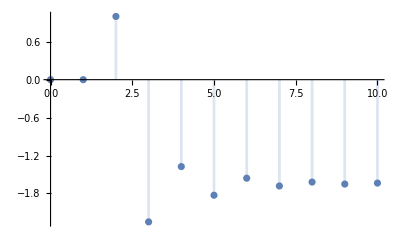

```mathematica
DiscretePlot[Subscript[y, f][k],{k,0,10},PlotRange->All]
```